```mathematica
(*Початоква купа формул*)
ClearAll[x,t,L,Gtailor,G,y,u,uI,t1,t2,x1,x2,T,TI,X,XI,Gx]
L=(D[#,t]-D[#,{x,2}])&
G=(t/Sqrt[4Pi*t]*Exp[-x^2/(4t)])(*/.{t->(t-tI),x->(x-xI)}*)
Gtailor=Simplify[Normal[Series[G,{x,1,2},{t,5,2}]]]/.{t->(t-tI),x->(x-xI)}
G=G/.{t->(t-tI),x->(x-xI)}
y:=Sin[x]*Sin[t]
u := L[y]
uI:=u/.{x->xI,t->tI}
(*Просторово-часова область*)
t1:=1
t2:=50
x1:=1
x2:=50
T:={t,t1,t2}
TI:=T/.{t->tI}
X:={x,x1,x2}
XI:=X/.{x->xI}
```

∂_t #1-∂_{x,2} #1&

(ⅇ^(-x^2/(4 t)) √t)/(2 √π)

(-(t-tI)^2 (19989+2802 (x-xI)+1009 (x-xI)^2)+10 (t-tI) (61609+3962 (x-xI)+2229 (x-xI)^2)-25 (-65571+6722 (x-xI)+10649 (x-xI)^2))/(1600000 ⅇ^(1/20) √(5 π))

(ⅇ^(-(x-xI)^2/(4 (t-tI))) √(t-tI))/(2 √π)

1/(230400000000000 ⅇ^(1/20) √(5 π))(-38564587639+3492326196 x-19899823554 x^2+6047283076 x^3+637041921 x^4-20 (-53838648659+4150521476 x-24935027274 x^2+7179668756 x^3+862925701 x^4)+150 (-89359748879+5111785556 x-33572242194 x^2+8830227236 x^3+1268618281 x^4)-500 (-266290016299+6645110436 x-52375276314 x^2+11456110516 x^3+2133911661 x^4)+625 (262967461081+9464928116 x-137190497634 x^2+16267110596 x^3+4664037841 x^4))

(ⅇ^(-x^2/4))/(2 √π)

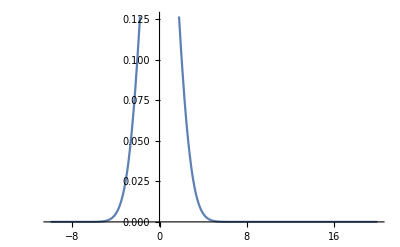

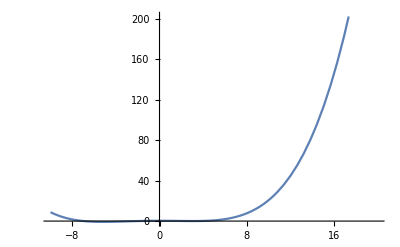

```mathematica
Gtailorx=Gtailor/.{t->1,tI->0,xI->0}
Gx=G/.{t->1,tI->0,xI->0}
Plot[Gx, {x,-10,20}]
Plot[Gtailorx, {x,-10,20}]
```

(97608150000000+149215080000000 t-16158204000000 t^2+1331611200000 t^3-48287760000 t^4)/(230400000000000 ⅇ^(1/20) √(5 π))

(ⅇ^(-1/4/t) √t)/(2 √π)

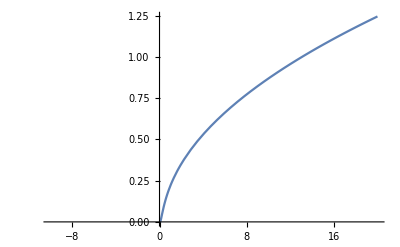

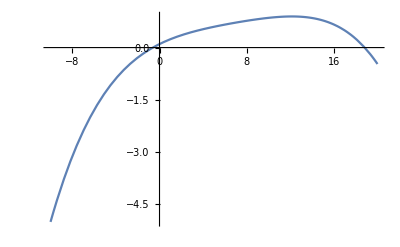

```mathematica
Gtailort=Gtailor/.{x->1,tI->0,xI->0}
Gt=G/.{x->1,tI->0,xI->0}
Plot[Gt, {t,-10,20}]
Plot[Gtailort, {t,-10,20}]
```

```mathematica
Gtailor*uI
```

1/(1600000 ⅇ^(1/20) √(5 π))(-(t-tI)^2 (19989+2802 (x-xI)+1009 (x-xI)^2)+10 (t-tI) (61609+3962 (x-xI)+2229 (x-xI)^2)-25 (-65571+6722 (x-xI)+10649 (x-xI)^2)) (Cos[tI] Sin[xI]+Sin[tI] Sin[xI])

```mathematica
(*Перший у*)
yInf=Simplify[Integrate[Gtailor*uI,Evaluate[XI],Evaluate[TI]]]
```

1/(3200000 ⅇ^(1/20) √(5 π))(-9463760809+2495620 Cos[2]+741175112 Cos[49]+682151440 Cos[51]-8679566489 Cos[100]-582260 Sin[2]+670366844 Sin[49]-2 t^2 (Cos[1]-Cos[50]-Sin[1]+Sin[50]) (16178 Cos[1]+1009 x^2 (Cos[1]-Cos[50])-2400371 Cos[50]+784 Sin[1]+x (784 Cos[1]+98098 Cos[50]+2018 (Sin[1]-Sin[50]))+98098 Sin[50])-859127304 Sin[51]+10030216217 Sin[100]+x^2 (-4041215-263198 Cos[2]+4041215 Cos[49]+4041215 Cos[51]-3778017 Cos[100]+311814 Sin[2]-3712583 Sin[49]-4336211 Sin[51]+4024397 Sin[100])-2 x (-189006124+128438 Cos[2]+16779993 Cos[49]+8107571 Cos[51]-180462140 Cos[100]+449966 Sin[2]+19690209 Sin[49]-18797133 Sin[51]+200263734 Sin[100])+2 t (151151624+276178 Cos[2]-29480949 Cos[49]-26974185 Cos[51]+138678246 Cos[100]-311926 Sin[2]-29725703 Sin[49]+34119419 Sin[51]+x^2 (71731+11145 Cos[2]-71731 Cos[49]-71731 Cos[51]+60586 Cos[100]-13163 Sin[2]+49441 Sin[49]+75767 Sin[51]-62604 Sin[100])-155478168 Sin[100]+2 x (-3027753+11923 Cos[2]+605144 Cos[49]+453610 Cos[51]-2888142 Cos[100]+11601 Sin[2]+713636 Sin[49]-698422 Sin[51]+3109430 Sin[100])))

```mathematica
(*Точки для подбудови вектори U*)
(*m0:={{xI->1,tI->-10},{xI->2,tI->-20},{xI->3,tI->-30},{xI->4,tI->-1},{xI->5,tI->-2}}
mE:={{xI->100,tI->1},{xI->200,tI->30},{xI->55,tI->10},{xI->65,tI->20},{xI->75,tI->30}}*)
m0:={{xI->1,tI->-10},{xI->2,tI->-20}}
size0:=Length[m0]
mE:={{xI->100,tI->1},{xI->200,tI->30}}
sizeE:=Length[mE]

(* Області (початкова і гранична) *)
region0:=Boole[t==0&&x≠x2&&x≠x1]
regionE:=Boole[t!=0&&x==x2&&x==x1]
```

```mathematica
Gm0:=G/.m0
GmE:=G/.mE
```

```mathematica
(*Вектор В*)
B11:=Gm0*region0
B12:=GmE*region0
B21:=Gm0*regionE
B22:=GmE*regionE
B:={Join[B11,B12],Join[B21,B22]}
B//MatrixForm
Transpose[B]//MatrixForm
```

((ⅇ^(-x^2/(4 t)) √t Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-x^2/(4 t)) √t Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-x^2/(4 t)) √t Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-x^2/(4 t)) √t Boole[t==0&&x≠50&&x≠1])/(2 √π)
(ⅇ^(-x^2/(4 t)) √t Boole[t≠0&&x==50&&x==1])/(2 √π) | (ⅇ^(-x^2/(4 t)) √t Boole[t≠0&&x==50&&x==1])/(2 √π) | (ⅇ^(-x^2/(4 t)) √t Boole[t≠0&&x==50&&x==1])/(2 √π) | (ⅇ^(-x^2/(4 t)) √t Boole[t≠0&&x==50&&x==1])/(2 √π))

((ⅇ^(-x^2/(4 t)) √t Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-x^2/(4 t)) √t Boole[t≠0&&x==50&&x==1])/(2 √π)
(ⅇ^(-x^2/(4 t)) √t Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-x^2/(4 t)) √t Boole[t≠0&&x==50&&x==1])/(2 √π)
(ⅇ^(-x^2/(4 t)) √t Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-x^2/(4 t)) √t Boole[t≠0&&x==50&&x==1])/(2 √π)
(ⅇ^(-x^2/(4 t)) √t Boole[t==0&&x≠50&&x≠1])/(2 √π) | (ⅇ^(-x^2/(4 t)) √t Boole[t≠0&&x==50&&x==1])/(2 √π))

```mathematica
(*Вектор У з областями*)
Y:={y*region0,y*regionE}
```

```mathematica
By=Integrate[(Transpose[B].Y)/.{t->0},Evaluate[X]]+Integrate[(Transpose[B].Y)/.{x->x1},Evaluate[T]]+Integrate[(Transpose[B].Y)/.{x->x2},Evaluate[T]]
```

```mathematica
P=PseudoInverse[Integrate[(Transpose[B].B)/.{t->0},Evaluate[X]]+Integrate[(Transpose[B].B)/.{x->x1},Evaluate[T]]+Integrate[(Transpose[B].B)/.{x->x2},Evaluate[T]]]
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

{{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate}}

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

PseudoInverse::mindet: Input matrix contains an indeterminate entry.

PseudoInverse[{{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate},{Indeterminate,Indeterminate,Indeterminate,Indeterminate}}]

```mathematica
u0=P[[1;;size0]].By
```

```mathematica
uE=P[[size0+1;;]].By
```

```mathematica
yFull=yInf+Gm0.u0+GmE.uE
yFull
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ⅇ^ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Indeterminate